```mathematica
SolIn[SolData_]:=(
sol=Flatten[Drop[Import[SolData,"Table"],1]]+1;
sol=Append[sol,sol[[1]]];
{ArcLength[Line[pts[[sol]]]]//N,sol}
)
```

```mathematica
pts=Drop[Drop[Import["eil51.tsp","Table"],6],-1][[All,2;;3]]
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

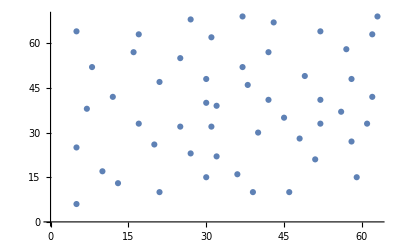

```mathematica
ListPlot[pts]
```

```mathematica
AbsoluteTiming[FindShortestTour[pts]]//N
```

{0.742824,{428.982,{1.,32.,11.,38.,5.,49.,10.,39.,33.,45.,15.,37.,17.,44.,42.,19.,40.,41.,13.,25.,14.,18.,4.,47.,12.,46.,51.,27.,6.,48.,23.,24.,43.,7.,26.,8.,31.,28.,3.,36.,35.,20.,29.,21.,34.,30.,9.,50.,16.,2.,22.,1.}}}

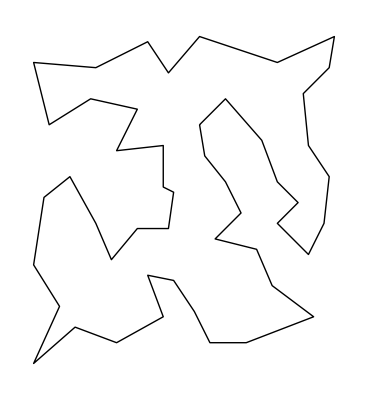

```mathematica
Graphics[Line[pts[[FindShortestTour[pts][[2]]]]]]
```

```mathematica
SolIn["eil51_greedy.sol"](*0.00s*)
```

{4659.05,{1,32,11,5,38,9,49,10,30,34,50,16,2,29,21,43,24,14,25,13,41,19,42,40,39,33,45,15,44,37,17,4,18,47,12,46,51,27,6,48,23,7,26,8,31,28,3,20,35,36,22,1}}

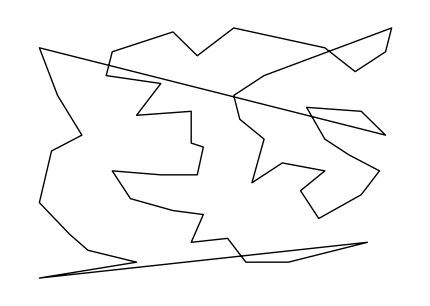

```mathematica
Graphics[Line[pts[[sol]]]]
```

```mathematica
SolIn["eil51_2opt.sol"](*0.00s*)
```

{451.829,{2,29,21,16,50,34,30,39,10,49,9,38,5,11,32,1,48,23,6,27,51,46,12,47,18,4,17,37,33,45,15,44,42,40,19,41,13,25,14,24,43,7,26,8,31,28,3,36,35,20,22,2}}

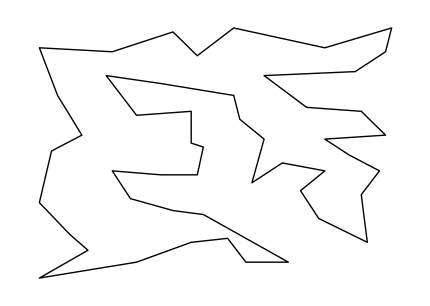

```mathematica
Graphics[Line[pts[[sol]]]]
```

```mathematica
SolIn["eil51_linkern.sol"](*0.06s*)
```

{429.983,{1,22,8,26,31,28,3,36,35,20,2,29,21,16,50,34,30,9,49,10,39,33,45,15,44,42,40,19,41,13,25,14,24,43,7,23,48,6,27,51,46,12,47,18,4,17,37,5,38,11,32,1}}

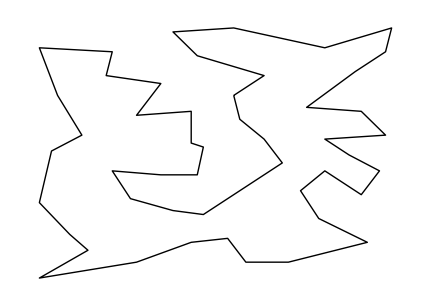

```mathematica
Graphics[Line[pts[[sol]]]]
```

```mathematica
SolIn["eil51_concorde.sol"]
```

{429.983,{1,22,8,26,31,28,3,36,35,20,2,29,21,16,50,34,30,9,49,10,39,33,45,15,44,42,40,19,41,13,25,14,24,43,7,23,48,6,27,51,46,12,47,18,4,17,37,5,38,11,32,1}}

```mathematica
Graphics[Line[pts[[sol]]]]
```

-Graphics-

```mathematica
pts=Drop[Drop[Import["a280.tsp","Table"],6],-1][[All,2;;3]]
```

{{288,149},{288,129},{270,133},{256,141},{256,157},{246,157},{236,169},{228,169},{228,161},{220,169},{212,169},{204,169},{196,169},{188,169},{196,161},{188,145},{172,145},{164,145},{156,145},{148,145},{140,145},{148,169},{164,169},{172,169},{156,169},{140,169},{132,169},{124,169},{116,161},{104,153},{104,161},{104,169},{90,165},{80,157},{64,157},{64,165},{56,169},{56,161},{56,153},{56,145},{56,137},{56,129},{56,121},{40,121},{40,129},{40,137},{40,145},{40,153},{40,161},{40,169},{32,169},{32,161},{32,153},{32,145},{32,137},{32,129},{32,121},{32,113},{40,113},{56,113},{56,105},{48,99},{40,99},{32,97},{32,89},{24,89},{16,97},{16,109},{8,109},{8,97},{8,89},{8,81},{8,73},{8,65},{8,57},{16,57},{8,49},{8,41},{24,45},{32,41},{32,49},{32,57},{32,65},{32,73},{32,81},{40,83},{40,73},{40,63},{40,51},{44,43},{44,35},{44,27},{32,25},{24,25},{16,25},{16,17},{24,17},{32,17},{44,11},{56,9},{56,17},{56,25},{56,33},{56,41},{64,41},{72,41},{72,49},{56,49},{48,51},{56,57},{56,65},{48,63},{48,73},{56,73},{56,81},{48,83},{56,89},{56,97},{104,97},{104,105},{104,113},{104,121},{104,129},{104,137},{104,145},{116,145},{124,145},{132,145},{132,137},{140,137},{148,137},{156,137},{164,137},{172,125},{172,117},{172,109},{172,101},{172,93},{172,85},{180,85},{180,77},{180,69},{180,61},{180,53},{172,53},{172,61},{172,69},{172,77},{164,81},{148,85},{124,85},{124,93},{124,109},{124,125},{124,117},{124,101},{104,89},{104,81},{104,73},{104,65},{104,49},{104,41},{104,33},{104,25},{104,17},{92,9},{80,9},{72,9},{64,21},{72,25},{80,25},{80,25},{80,41},{88,49},{104,57},{124,69},{124,77},{132,81},{140,65},{132,61},{124,61},{124,53},{124,45},{124,37},{124,29},{132,21},{124,21},{120,9},{128,9},{136,9},{148,9},{162,9},{156,25},{172,21},{180,21},{180,29},{172,29},{172,37},{172,45},{180,45},{180,37},{188,41},{196,49},{204,57},{212,65},{220,73},{228,69},{228,77},{236,77},{236,69},{236,61},{228,61},{228,53},{236,53},{236,45},{228,45},{228,37},{236,37},{236,29},{228,29},{228,21},{236,21},{252,21},{260,29},{260,37},{260,45},{260,53},{260,61},{260,69},{260,77},{276,77},{276,69},{276,61},{276,53},{284,53},{284,61},{284,69},{284,77},{284,85},{284,93},{284,101},{288,109},{280,109},{276,101},{276,93},{276,85},{268,97},{260,109},{252,101},{260,93},{260,85},{236,85},{228,85},{228,93},{236,93},{236,101},{228,101},{228,109},{228,117},{228,125},{220,125},{212,117},{204,109},{196,101},{188,93},{180,93},{180,101},{180,109},{180,117},{180,125},{196,145},{204,145},{212,145},{220,145},{228,145},{236,145},{246,141},{252,125},{260,129},{280,133}}

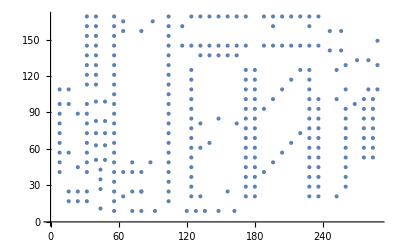

```mathematica
ListPlot[pts]
```

```mathematica
AbsoluteTiming[FindShortestTour[pts]]//N
```

{0.237899,{2586.77,{1.,2.,242.,243.,244.,241.,240.,239.,238.,237.,236.,235.,234.,233.,232.,231.,246.,245.,247.,250.,251.,230.,229.,228.,227.,226.,225.,224.,223.,222.,221.,220.,219.,218.,217.,216.,215.,214.,213.,212.,211.,210.,209.,252.,253.,208.,207.,206.,205.,204.,203.,202.,201.,200.,144.,143.,146.,145.,199.,198.,197.,196.,195.,194.,193.,192.,191.,190.,189.,188.,187.,186.,185.,184.,183.,182.,181.,176.,180.,179.,150.,178.,177.,151.,152.,156.,153.,155.,154.,129.,128.,127.,126.,30.,125.,124.,123.,122.,121.,120.,119.,157.,158.,159.,160.,175.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,107.,106.,105.,104.,103.,102.,101.,100.,99.,98.,97.,96.,95.,94.,93.,92.,91.,90.,89.,109.,108.,110.,111.,114.,115.,117.,116.,86.,85.,84.,87.,113.,112.,88.,83.,82.,81.,80.,79.,78.,77.,75.,76.,74.,73.,72.,71.,70.,69.,68.,67.,66.,65.,64.,58.,57.,56.,55.,54.,53.,52.,51.,50.,49.,48.,47.,46.,45.,44.,59.,63.,62.,118.,61.,60.,43.,42.,41.,40.,39.,38.,37.,36.,35.,34.,33.,32.,31.,29.,28.,27.,26.,22.,25.,23.,24.,14.,13.,15.,12.,11.,10.,9.,8.,7.,6.,5.,4.,277.,276.,275.,274.,273.,272.,271.,16.,17.,18.,19.,20.,21.,130.,131.,132.,133.,134.,270.,269.,135.,136.,268.,267.,137.,138.,139.,149.,148.,147.,142.,141.,140.,266.,265.,264.,263.,262.,261.,260.,259.,258.,257.,254.,255.,256.,249.,248.,278.,279.,3.,280.,1.}}}

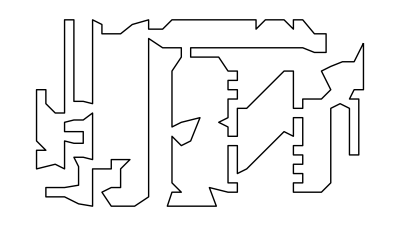

```mathematica
Graphics[Line[pts[[FindShortestTour[pts][[2]]]]]]
```

```mathematica
SolIn["a280_greedy.sol"](*0.00s*)
```

{3256.81,{1,2,280,3,279,278,4,277,276,275,274,273,272,271,16,263,262,261,260,259,258,257,256,255,254,253,252,209,210,211,214,215,218,219,222,221,220,217,216,213,212,207,208,206,205,204,203,202,200,144,143,142,141,140,265,264,242,243,248,249,233,234,235,236,237,232,231,238,239,246,245,240,241,244,247,250,251,230,229,228,227,226,225,224,223,51,50,49,52,53,48,47,54,55,46,45,56,58,57,44,59,68,69,92,91,90,89,109,110,108,104,103,102,101,100,99,98,93,94,95,96,97,180,179,178,150,149,137,136,135,134,270,269,268,267,266,138,139,148,147,146,145,199,198,201,196,195,194,197,193,192,191,190,189,188,186,187,185,184,183,182,181,176,177,151,152,156,153,155,154,126,127,128,129,130,131,132,133,18,17,19,20,21,33,34,35,36,37,38,39,40,41,42,43,60,61,118,62,63,64,65,66,67,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,116,115,117,87,113,114,111,112,88,107,105,106,173,174,172,171,170,169,168,167,166,165,164,163,162,161,175,160,159,158,157,119,120,121,122,123,124,125,30,31,32,29,28,27,26,22,25,23,24,14,13,15,12,11,10,8,7,9,6,5,1}}

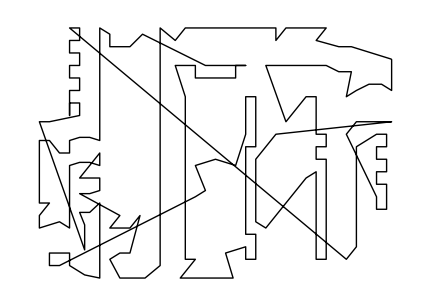

```mathematica
Graphics[Line[pts[[sol]]]]
```

```mathematica
SolIn["a280_2opt.sol"](*0.00s*)
```

{3190.98,{37,50,51,49,52,53,54,48,47,55,46,45,56,44,59,57,58,68,69,64,65,66,67,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,116,115,117,118,62,63,61,60,43,42,41,40,39,38,36,35,34,33,180,179,176,181,182,183,184,185,186,187,188,189,190,191,192,193,146,147,148,139,140,141,142,143,144,145,199,198,197,194,195,196,201,200,202,203,204,205,206,208,207,212,213,216,217,220,221,222,219,218,215,214,211,210,209,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,134,135,136,137,138,149,150,178,177,151,152,156,153,155,154,126,127,128,129,130,131,21,20,19,18,133,132,17,16,271,272,273,274,275,276,277,4,5,1,2,280,3,279,278,249,248,243,242,241,240,245,246,239,238,231,232,233,234,235,236,237,244,247,250,251,230,229,228,227,226,225,224,223,97,96,95,94,93,98,99,100,101,102,92,91,90,89,109,112,88,87,113,114,111,110,108,104,103,105,106,107,173,174,172,171,170,169,168,167,166,165,164,163,162,161,175,160,159,158,157,119,120,121,122,123,124,125,30,31,32,29,28,27,26,22,25,23,24,14,13,15,12,11,10,8,7,6,9,37}}

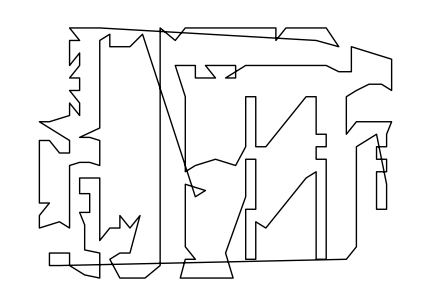

```mathematica
Graphics[Line[pts[[sol]]]]
```

```mathematica
SolIn["a280_linkern.sol"](*0.25s*)
```

{2586.77,{1,280,3,279,278,248,249,256,255,252,253,254,257,258,259,260,261,262,263,264,265,266,140,141,148,149,139,138,137,267,268,136,135,269,270,134,133,18,17,16,271,272,273,274,275,276,277,4,5,6,7,9,8,10,11,12,15,13,14,24,23,25,22,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,60,61,118,62,63,59,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,88,112,113,87,84,85,86,116,117,115,114,111,110,108,109,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,174,173,172,171,170,169,168,167,166,165,164,163,162,161,175,160,159,158,157,119,120,121,122,123,124,125,126,127,128,21,20,19,132,131,130,129,154,155,153,156,152,151,177,178,150,179,180,176,181,182,183,184,185,186,187,188,189,190,191,192,193,197,194,195,196,201,198,199,145,146,147,142,143,144,200,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,251,250,247,244,245,246,231,232,233,234,235,236,237,238,239,240,241,243,242,2,1}}

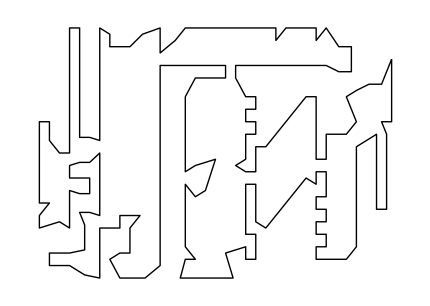

```mathematica
Graphics[Line[pts[[sol]]]]
```

```mathematica
pts=Drop[Drop[Import["pr439.tsp","Table"],6],-1][[All,2;;3]];
```

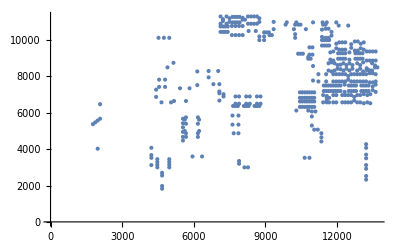

```mathematica
ListPlot[pts]
```

```mathematica
AbsoluteTiming[FindShortestTour[pts]]//N
```

{1.23273,{107378.,{1.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,33.,34.,35.,36.,37.,38.,39.,40.,41.,43.,42.,44.,45.,46.,49.,47.,48.,50.,51.,53.,54.,55.,56.,82.,81.,80.,79.,57.,58.,78.,86.,87.,77.,59.,60.,61.,76.,75.,62.,32.,31.,30.,28.,26.,27.,29.,63.,73.,74.,64.,25.,23.,21.,22.,24.,65.,66.,67.,20.,19.,18.,68.,69.,70.,71.,72.,88.,89.,90.,91.,104.,105.,106.,107.,108.,109.,110.,111.,112.,146.,144.,147.,148.,145.,185.,190.,224.,223.,222.,233.,234.,235.,236.,237.,238.,239.,240.,221.,220.,219.,218.,217.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,210.,211.,212.,213.,214.,215.,216.,198.,197.,196.,195.,194.,193.,191.,184.,192.,183.,182.,181.,180.,179.,157.,156.,155.,154.,153.,151.,150.,143.,152.,142.,141.,140.,139.,138.,158.,159.,160.,161.,162.,163.,134.,135.,136.,137.,124.,126.,127.,129.,125.,123.,101.,122.,121.,119.,120.,117.,115.,118.,116.,113.,114.,103.,102.,92.,93.,94.,100.,95.,96.,97.,98.,99.,128.,130.,131.,132.,133.,167.,165.,164.,166.,169.,168.,170.,171.,172.,173.,174.,204.,175.,176.,177.,178.,199.,200.,201.,202.,203.,205.,206.,207.,208.,209.,251.,253.,252.,255.,254.,316.,315.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,331.,332.,330.,303.,302.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,301.,273.,274.,275.,276.,277.,278.,279.,294.,295.,296.,297.,298.,299.,300.,333.,334.,335.,336.,337.,338.,339.,360.,370.,361.,362.,363.,364.,365.,366.,367.,368.,369.,378.,385.,386.,387.,388.,401.,400.,402.,404.,405.,417.,418.,428.,429.,431.,416.,415.,419.,420.,421.,414.,406.,407.,413.,412.,423.,422.,432.,433.,430.,427.,424.,426.,425.,410.,411.,409.,408.,403.,434.,438.,437.,436.,435.,439.,284.,344.,343.,342.,341.,373.,371.,372.,383.,382.,384.,394.,395.,393.,397.,396.,398.,399.,392.,391.,381.,375.,374.,380.,390.,389.,379.,377.,376.,345.,346.,348.,347.,349.,350.,351.,353.,352.,354.,355.,356.,358.,357.,359.,293.,292.,291.,290.,289.,288.,340.,287.,286.,285.,280.,232.,231.,225.,189.,188.,187.,230.,281.,282.,229.,283.,228.,227.,226.,186.,149.,85.,84.,83.,52.,2.,3.,1.}}}

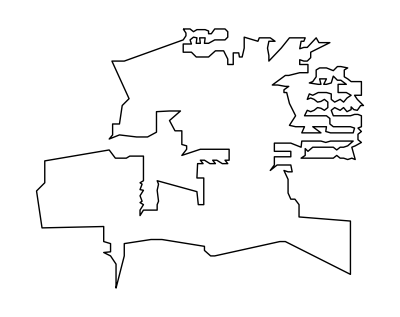

```mathematica
Graphics[Line[pts[[FindShortestTour[pts][[2]]]]]]
```

```mathematica
SolIn["pr439_greedy.sol"](*0.01s*)
```

{124130.,{1,3,2,52,51,50,48,47,49,46,45,43,41,40,38,39,42,44,87,86,78,77,59,60,61,76,75,62,32,31,30,439,435,436,437,438,434,403,408,409,411,410,425,424,426,413,412,423,422,427,430,433,432,431,429,428,418,417,405,404,402,221,220,219,218,217,216,215,214,213,212,211,210,250,251,209,253,252,249,248,247,246,245,244,243,242,241,240,239,238,237,236,235,234,233,222,223,224,190,185,145,148,147,146,144,108,109,112,111,110,74,73,63,28,29,27,26,64,25,23,24,22,21,20,19,18,69,68,67,66,65,72,71,70,91,90,89,88,107,106,105,104,102,92,93,94,101,100,95,96,98,97,133,132,131,130,128,99,125,123,124,126,127,129,134,135,136,137,138,139,140,141,142,116,118,119,121,122,120,117,115,103,114,113,143,152,151,150,153,154,155,156,157,158,159,177,178,179,180,181,182,183,192,184,191,193,194,195,196,197,198,199,200,201,202,203,205,206,207,208,171,172,174,173,204,175,176,160,161,162,163,164,165,167,166,169,170,168,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,331,330,332,273,274,275,276,277,278,279,294,295,296,297,298,299,300,333,334,335,336,337,338,339,370,360,361,362,363,364,365,366,367,368,369,378,385,386,387,388,401,400,416,415,419,420,421,414,406,407,396,397,398,393,394,395,384,383,382,371,372,373,374,375,381,391,392,399,390,389,379,380,376,377,345,346,348,349,347,350,351,353,354,352,355,356,358,359,357,293,292,291,290,289,288,340,287,286,285,280,232,231,225,188,189,187,230,281,282,341,342,343,344,284,283,228,229,226,227,186,149,83,84,85,53,54,55,56,82,81,80,79,57,58,37,36,35,34,33,17,16,15,14,13,12,11,10,9,8,7,6,5,4,1}}

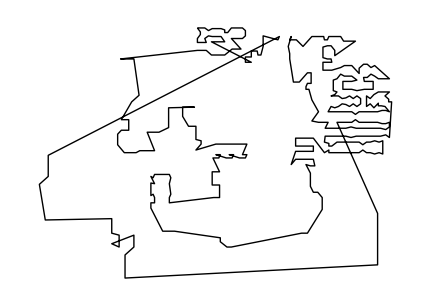

```mathematica
Graphics[Line[pts[[sol]]]]
```

```mathematica
SolIn["pr439_2opt.sol"](*0.01s*)
```

{122156.,{96,95,100,101,94,93,92,102,104,105,106,107,88,89,90,91,70,71,72,65,66,67,68,69,18,19,20,21,22,24,23,25,28,29,27,26,64,320,321,322,323,324,325,326,327,328,329,331,330,332,273,274,275,276,277,278,279,294,295,296,297,298,299,300,333,334,335,336,337,338,339,360,370,361,362,363,364,365,366,367,368,369,378,385,386,387,388,401,400,416,415,419,420,421,414,406,407,396,397,398,393,395,394,384,382,383,372,371,373,374,375,381,391,392,399,390,389,379,380,376,377,345,346,347,348,349,350,351,353,354,352,355,356,358,357,359,293,292,291,290,289,288,340,287,286,285,280,232,231,225,189,188,187,230,281,282,341,342,343,344,284,283,228,229,227,226,186,149,83,84,85,439,435,436,437,438,434,403,408,409,411,410,425,424,426,413,412,423,422,427,430,433,432,431,429,428,418,417,405,404,402,319,318,317,316,315,314,313,312,311,310,309,308,307,306,305,304,303,302,301,272,271,270,269,268,267,266,265,264,263,262,261,260,259,258,257,256,254,255,252,249,248,247,246,245,244,243,242,241,240,239,238,237,236,235,234,233,222,223,224,190,185,145,148,147,146,144,108,109,112,111,110,74,73,63,31,30,32,62,75,76,61,60,59,58,57,79,80,81,82,56,55,54,53,51,50,48,47,44,42,39,38,40,41,43,45,46,49,52,2,3,1,4,5,6,7,8,9,10,11,12,13,14,15,16,17,33,34,35,36,37,86,78,77,87,221,220,219,218,217,216,215,214,213,212,211,210,250,251,253,209,208,207,171,170,168,169,166,167,165,164,163,162,160,161,175,176,204,174,173,172,206,205,203,202,201,200,199,198,197,196,195,194,193,191,184,192,183,182,181,180,179,178,177,159,158,157,156,155,154,153,152,151,150,143,113,114,103,115,117,120,122,121,119,118,116,142,141,140,139,138,137,136,135,134,129,127,126,124,123,125,99,128,130,131,132,133,97,98,96}}

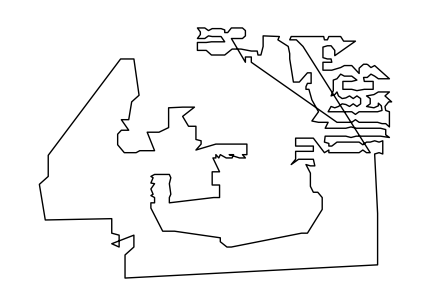

```mathematica
Graphics[Line[pts[[sol]]]]
```

```mathematica
SolIn["pr439_linkern.sol"](*1.13s*)
```

{107249.,{1,3,2,52,83,84,85,149,186,226,227,228,283,229,282,281,230,187,188,189,225,231,232,280,285,286,287,340,288,289,290,291,292,293,359,357,358,356,355,354,352,353,351,350,349,347,348,346,345,376,377,379,389,390,380,374,375,381,391,392,399,398,396,397,393,395,394,384,382,383,372,371,373,341,342,343,344,284,439,435,436,437,438,434,403,408,409,411,410,425,426,424,427,430,433,432,422,423,412,413,407,406,414,421,420,419,415,416,431,429,428,418,417,405,404,402,400,401,388,387,386,385,378,369,368,367,366,365,364,363,362,361,370,360,339,338,337,336,335,334,333,300,299,298,297,296,295,294,279,278,277,276,275,274,273,301,272,271,270,269,268,267,266,265,264,263,262,261,260,259,258,257,256,314,313,312,311,310,309,308,307,306,305,304,302,303,330,332,331,329,328,327,326,325,324,323,322,321,320,319,318,317,315,316,254,255,252,253,251,209,208,207,206,205,203,202,201,200,199,198,197,196,195,194,193,192,183,182,181,180,179,178,177,176,175,204,174,173,172,171,170,168,169,166,164,165,167,133,132,131,130,128,129,127,126,124,123,125,99,98,97,96,95,100,94,93,92,102,103,115,117,120,101,122,121,119,118,116,114,113,143,152,142,141,140,139,138,137,136,135,134,163,162,161,160,159,158,157,156,155,154,153,151,150,184,191,222,221,220,219,218,217,216,215,214,213,212,211,210,250,249,248,247,246,245,244,243,242,241,240,239,238,237,236,235,234,233,223,224,190,185,145,148,147,144,146,112,111,110,109,108,107,106,105,104,91,90,89,88,72,71,70,69,68,18,19,20,67,66,65,24,22,21,23,25,64,74,73,63,29,27,26,28,30,31,32,62,75,76,61,60,59,77,87,86,78,58,57,79,80,81,82,56,55,54,53,51,50,48,47,49,46,45,44,42,43,41,40,39,38,37,36,35,34,33,17,16,15,14,13,12,11,10,9,8,7,6,5,4,1}}

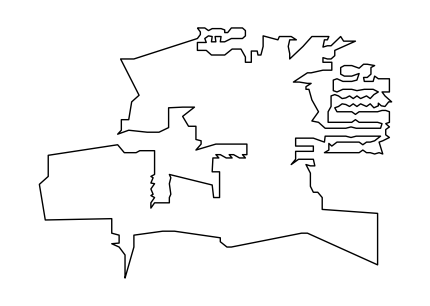

```mathematica
Graphics[Line[pts[[sol]]]]
```